```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/home/gercklim/WORK_DIRECTORY/7_СЕМ/ТПВ/PCT/Lab_4/VISUALIZATION

```mathematica
res1 = Reverse@Import["RESULT.txt", "Table"];
```

```mathematica
data = Table[{res1[[i]][[1]], res1[[i]][[2]], (res1[[1]][[2]])/(res1[[i]][[2]])} ,{i, 1, Length@res1}];
```

```mathematica
data = Prepend[ data,{"Потоки","Время","Ускорение"}];
Grid[data,Frame->All, Spacings->{1, 2}, ItemSize->{8, 2}]
```

Потоки | Время | Ускорение
1 | 385.478 | 1.
2 | 195.303 | 1.97374
4 | 101.57 | 3.7952
8 | 51.8942 | 7.42815
8 | 51.8802 | 7.43016
16 | 29.9543 | 12.8689
24 | 19.9169 | 19.3543
32 | 15.0786 | 25.5646
48 | 9.6143 | 40.0942
64 | 8.13696 | 47.3737

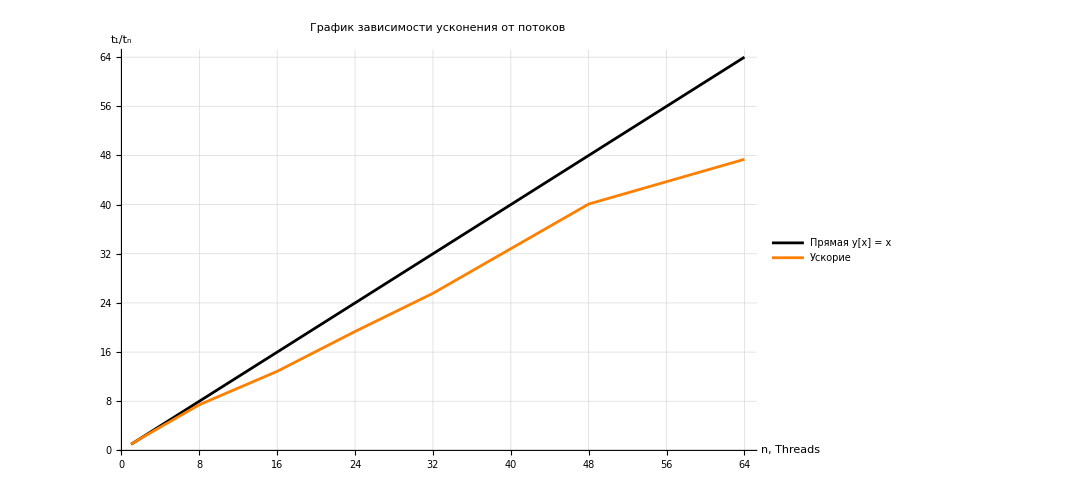

```mathematica
Show[
Plot[x, {x, 1, 64}, PlotStyle->Black, PlotLegends->{"Прямая y[x] = x"}],
ListLinePlot[Table[{data[[i]][[1]],(data[[2]][[2]])/(data[[i]][[2]])},{i,2,Length@data}],PlotStyle->Orange,PlotLegends->{"Ускорие"}],
GridLines->Automatic,AspectRatio->1/GoldenRatio,Axes->True,AxesStyle->{{Arrowheads[0.025],Black},{Arrowheads[0.03],Black}},
AxesLabel->{Style["n, Threads",Black,16,FontFamily->"Times"],Style["\!\(\*SubscriptBox[\(t\), \(1\)]\)/\!\(\*SubscriptBox[\(t\), \(n\)]\)",Black,16,FontFamily->"Times"]},LabelStyle->Directive[Black,14,FontFamily->"Times"],ImageSize->{800,500},PlotRange->All,PlotLabel->"График зависимости усконения от потоков"]
```